# The Edge of Random Tensor Eigenvalues with Deviation: Compilation of codes

## 1. Analytical expressions

### Signed distribution

```mathematica
Uabz[a_,b_,z_]:=Gamma[b-1]/Gamma[a] z^(1-b)Hypergeometric1F1[a-b+1,2-b,z]+Gamma[1-b]/Gamma[a-b+1] Hypergeometric1F1[a,b,z];
```

```mathematica
DZperp[L_,v_,α_]:=(3α/(2 v^2))^(1-L/2) D[k Uabz[1-L/2,3/2,3α k^2/(2 v^2)],k]/.k->1
```

```mathematica
Zperp[L_,v_,α_]:=(3α/(2 v^2))^(1-L/2) k Uabz[1-L/2,3/2,3α k^2/(2 v^2)]/.k->1
```

```mathematica
volSphere[L_]:=2 Pi^((L+1)/2)/Gamma[(L+1)/2]
```

```mathematica
eS0[v_,b_,L_,α_]:=Exp[-α v^2/(v^4+4 α b)]/Sqrt[(3 v^4+12 α b)(v^4+12 α b)^(L-1)]
```

```mathematica
rhoS[v_,b_,L_,α_]:=-((v^4-4 α b)/(v^4+4α b)Zperp[L,v,α]+8b v^2/(v^4+12 α b)DZperp[L,v,α])eS0[v,b,L,α]
```

```mathematica
rhoRadial[v_,b_,L_,α_]:=rhoS[v,b,L,α] volSphere[L-1]Abs[v]^(L-1) Sqrt[12 Pi α]^L/(2 Pi )^L
```

### Genuine distribution

```mathematica
rhoSizeBA[L_,v_,p_]:=2 Sqrt[L]/v^2 (p-1)^((L-1)/2)Exp[-(p-2)/(4 (p-1)v^2)] rhoMat[L,-Sqrt[p/(2(p-1))]/(Sqrt[L] v)]
```

```mathematica
cNp[L_,p_]:=2L Sqrt[2(p-1)^L/p];
phi[p_,x_]:=-(p-2) x^2/(2p);
phiHerm[j_,x_]:=HermiteH[j,x] Exp[-x^2/2]/Sqrt[2^j j! Sqrt[Pi]];
alphaFun[L_,x_]:=If[IntegerQ[L/2],0,phiHerm[(L-1),Sqrt[L]x]/(NIntegrate[phiHerm[(L-1),Sqrt[L]t],{t,-Infinity,Infinity}])];
rhoMat[L_,x_]:=(L phiHerm[L,Sqrt[L] x]^2-Sqrt[L(L+1)]phiHerm[L-1,Sqrt[L] x]phiHerm[L+1,Sqrt[L] x]+Sqrt[L/2]phiHerm[L-1,Sqrt[L] x]NIntegrate[Sign[Sqrt[L] x -t]/2 phiHerm[L,t],{t,-Infinity,Infinity}]+alphaFun[L,x])/Sqrt[L];
```

```mathematica
datTableLarge[alpha_,beta_,vmin_,vEnd_]:=Module[{q11,q22,q12,x1,gam1,gam2,gam3,intvalLarge,intLarge,x,g},
Clear[x,g];
q11=Sqrt[4 x1-1]/(2 x1);q22=-Sqrt[4 x1-1]/(2 x1);q12=-1/(2x1);

intLarge[x_,g_]=(-(gam3 (L-1))^2 q11 q22+(gam1-(L-1) gam3 q12+Sqrt[2 gam2] g)^2)^(1/2)Exp[-g^2] /. x1->x^2 (L-1)/(3 alpha) /. {gam1->(x^4-4 alpha beta)/(x^4+4 alpha beta),gam2->8 beta x^2/(x^4+4 alpha beta),gam3->8 beta x^2/(x^4+12 alpha beta)} ;

intvalLarge[x_]:=NIntegrate[intLarge[x,g],{g,-Infinity,Infinity}]/Sqrt[Pi];

Table[{xval,intvalLarge[xval]},{xval,vmin,vEnd,.01}]];
datTableSmall[alpha_,beta_,vmin_,vEnd_]:=Module[{q11,q22,q12,x1,gam1,gam2,gam3,x,g,intSmall,intvalSmall},
Clear[x,g];
q11=(1-Sqrt[1-4 x1])/(2 x1 Sqrt[1-4 x1]);q22=0;q12=(1-Sqrt[1-4 x1]-4 x1)/(2 x1 Sqrt[1-4 x1]);

(*Clear[x,int,beta,gam1,gam2,gam3]*)

intSmall[x_,g_]=((gam1-(L-1) gam3 q12+Sqrt[2 gam2] g)^2)^(1/2)Exp[-g^2] /. x1->x^2 (L-1)/(3 alpha) /. {gam1->(x^4-4 alpha beta)/(x^4+4 alpha beta),gam2->8 beta x^2/(x^4+4 alpha beta),gam3->8 beta x^2/(x^4+12 alpha beta)} ;

intvalSmall[x_]:=NIntegrate[intSmall[x,g],{g,-Infinity,Infinity}]/Sqrt[Pi];

Table[{xval,intvalSmall[xval]},{xval,vmin,vEnd,.001}]];
```

```mathematica
L=10;
alpha=1/2;beta=1;
epsilon=.001;
vStar=Sqrt[3/(8 (L-1))];
vmin=vStar+epsilon;
vEnd=10;
```

```mathematica
intdataLarge=Interpolation[datTableLarge[alpha,beta,vmin,vEnd]];
zParaLarge[x_]=intdataLarge[x];
```

```mathematica
intdataSmall=Interpolation[datTableSmall[alpha,beta,0,vStar-epsilon]];
zParaSmall[x_]=intdataSmall[x];
```

```mathematica
rhoVUnsigned[v_,L_,alpha_,beta_,vmin_,eps_]:=Sqrt[(v^4/(v^4+12 alpha beta))^(L-1) v^4/(v^4+4 alpha beta)] Exp[alpha/v^2-alpha v^2/(v^4+4alpha beta)]Piecewise[{{zParaLarge[v],v>vmin+eps },{zParaSmall[v],v<vmin -eps}}]rhoSizeBA[L,v,3]
```

General::munfl: Exp[-2.99526×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.98577×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

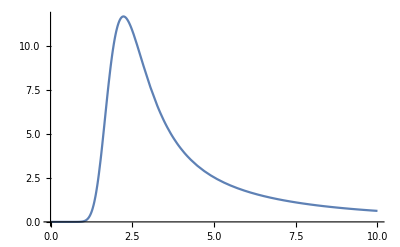

```mathematica
Plot[rhoVUnsigned[v,L,alpha,beta,vStar,epsilon],{v,0,10},PlotRange->Automatic]
```

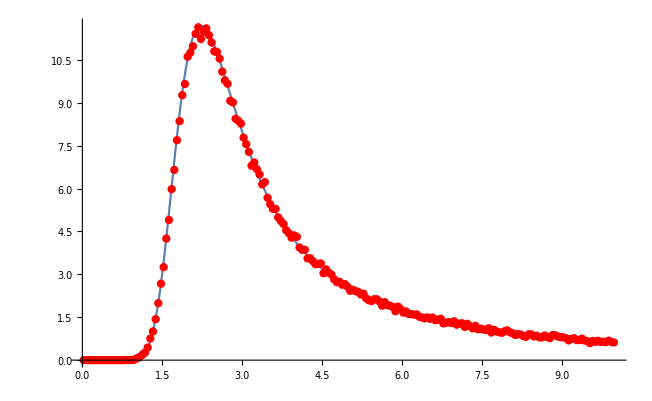

```mathematica
Show[%125,%138]
```

### Genuine distribution: Naoki’s code

```mathematica
Lval=10; (* Value of N *)

al=1/2; (* This cannot be changed, because ABC is normalized by that.*)

Clear[p,x,v,g,s,f,rho,coeff,aln,part]

p[j_,v_]:=(2^j j! Sqrt[Pi])^(-1/2) HermiteH[j,v] Exp[-v^2/2];

g[n_]:=1/2(-Integrate[p[n,t],{t,v,Infinity},Assumptions->v>0]+Integrate[p[n,t],{t,-Infinity,v},Assumptions->v>0]);

s[n_]:=Sum[p[i,v]^2,{i,0,n-1}];

aln[n_]:=Which[Mod[n,2]==0,0,True,
m=(n-1)/2;
p[2m,v]/Integrate[p[2m,t],{t,-Infinity,Infinity}]
]

f[n_]:=(s[n]+(n/2)^(1/2) p[n-1,v] g[n]+aln[n])/Sqrt[n];

Clear[rhod];
q=3;

(* ABC result *)
rhod[n_]:=2 Sqrt[n]/v^2(q-1)^((n-1)/2) Exp[-(q-2)/(4 (q-1) v^2)] (f[n]/. v->-y*Sqrt[3/(2*2)]/. y->1/v);


Clear[gam1,gam2,gam3,L];

q11=Sqrt[4x-1]/(2 Sqrt[eps] x)-1/(2x);
q12=-1/(2x)+Sqrt[eps]/(2 x Sqrt[4x-1]);
q21=q12;
q22=-Sqrt[eps]Sqrt[4x-1]/(2x)+eps/(2x);

intz2=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

q11=(1-Sqrt[1-4x])/(2 x Sqrt[1-4x]);
q12=(1-Sqrt[1-4x]-4x)/(2x Sqrt[1-4x]);
q21=q12;
q22=0;

intz1=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

intz1=Simplify[intz1 /. x->(L-1) v^2 / 3 /al ];

intz2=Simplify[intz2 /. x->(L-1) v^2 / 3 /al ];


gam1=(v^4-4 al be)/(v^4+4 al be);
gam2=8 be v^2/(v^4+4 al be);
gam3=8 be v^2/(v^4+12 al be);

Clear[nintz1,nintz2,zpara];

nintz1[v_,be_,L_]=intz1 ;
nintz2[v_,be_,L_]=intz2 ;

zpara[v_,be_,L_]:=1/Sqrt[Pi]*
Which[(L-1)v^2/(3 al)>1/4, NIntegrate[Exp[-y^2] Sqrt[nintz2[v,be,L]],{y,-Infinity,Infinity}],
True,NIntegrate[Exp[-y^2] Sqrt[nintz1[v,be,L]],{y,-Infinity,Infinity}]]


Clear[rhoalld,rhoalld1];

rhoalld1[v_,be_]=Expand[Simplify[rhod[Lval]*(v^4/(v^4 +4 al be ))^(1/2) ( v^4/(v^4 +12al be ))^((Lval-1)/2) Exp[- al v^2/(v^4+4 al be)+al /v^2],Assumptions->v>0]];

(* rho  be is beta, not betabar *)
rhoalld[v_,be_]:= zpara[v,be,Lval]*rhoalld1[v,be]
```

General::munfl: Exp[-8.98577×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

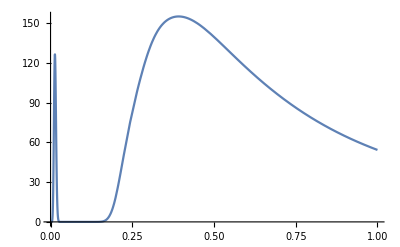

```mathematica
beval=.001/Lval^2;

g1=Plot[rhoalld[v,beval],{v,0,1},PlotRange->All]
```

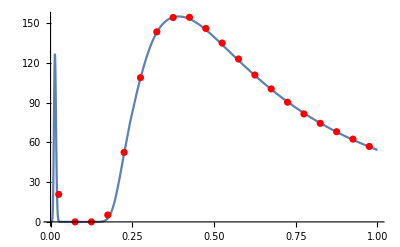

```mathematica
Show[g1,histoPlot]
```

General::munfl: Exp[-8.98577×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

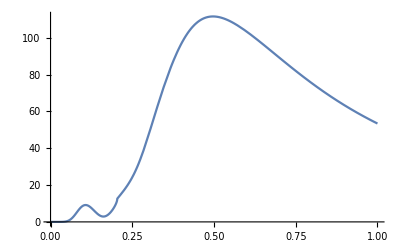

```mathematica
beval=.069/Lval^2;

g1=Plot[rhoalld[v,beval],{v,0,1},PlotRange->All]
```

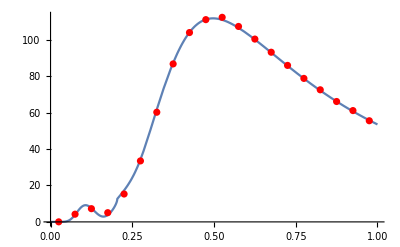

```mathematica
Show[g1,histoPlot]
```

General::munfl: Exp[-8.98577×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

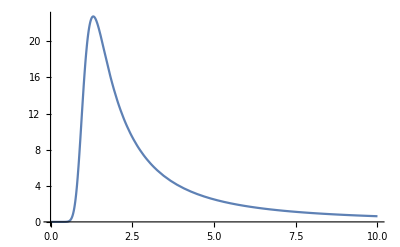

```mathematica
beval=.1;

g1=Plot[rhoalld[v,beval],{v,0,10},PlotRange->All]
```

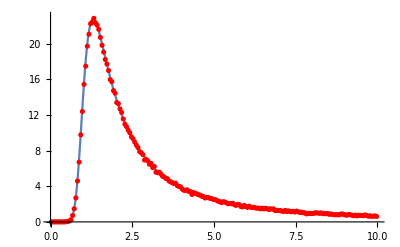

```mathematica
Show[g1,histoPlot]
```

```mathematica
L
```

L

```mathematica
Lval
```

10

```mathematica
beval=.01/Lval^2;
```

General::munfl: Exp[-9.98419×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

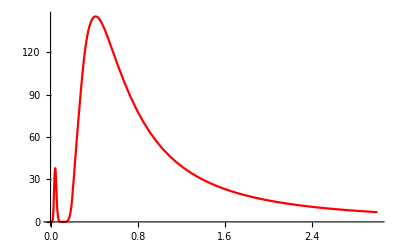

```mathematica
g1=Plot[rhoalld[v,beval],{v,0,3},PlotRange->All,PlotStyle->Red]
```

```mathematica
Show[g1,analPlot,PlotRange->{{0,1},{0,50}}]
```

## 2. Numerical simulations

### Data generation

```mathematica
L=10; (*N*)

(*betabar=0.001;*)

sampnum=10000; (*Number of sampling*);

filename=StringJoin["unsignedv2L",ToString[L],"samp",ToString[sampnum],"bb0001.m"];

Clear[sym,z,w,beta];

sym[i_]:=Which[i[[1]]==i[[2]]==i[[3]],1,i[[1]]==i[[2]]||i[[2]]==i[[3]]||i[[3]]==i[[1]],3,True,6];

w=Table[z[i],{i,1,L}];

beta=0.001/L^2;

dev=Sqrt[2 beta];

cut=10^(-13);

time=AbsoluteTime[];

list={};

listtest={};

SetSharedVariable[list,listtest];

ParallelDo[c=Table[0,{L},{L},{L}];
Do[c[[i,j,k]]=Sqrt[sym[{i,j,k}]] RandomVariate[NormalDistribution[0,1]],{i,1,L},{j,i,L},{k,j,L}];
c=Normal[Symmetrize[c]];
devvec=RandomVariate[NormalDistribution[0,dev],L];
eqs=w-c.w.w-devvec;
wsol=NSolve[eqs==0,w];
AppendTo[listtest,Length[wsol]];
Do[w0=w/. wsol[[solnum]];
If[Im[w0].Im[w0]<cut&&Re[w0].Re[w0]>cut,AppendTo[list,{Sqrt[Re[w0].Re[w0]],1}]],{solnum,1,Length[wsol]}];,{sampnum}];

Print["time=",AbsoluteTime[]-time];

Export[filename,list,OverwriteTarget->"KeepBoth"];
```

### Data analysis: Genuine distribution with legends and errors -- L=10 b=0.001/L^2

```mathematica
L=10;sampnum=10000;filename="unsignedv2L"<>ToString[L]<>"samp"<>ToString[sampnum]<>"b1.m";
```

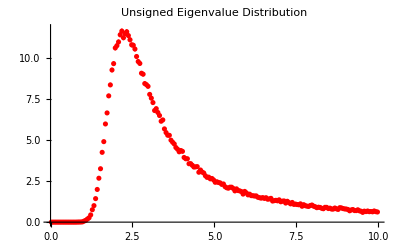

```mathematica
list=Import[NotebookDirectory[]<>filename];
(* Analysis of data *)

wmax=10; (* The range of |v| to see *)
dw=.05; (* Bin size *)

binmax=Ceiling[wmax/dw];

histo=Table[0,{binmax}];

Do[
vert=Ceiling[list[[datnum,1]]/dw];

If[vert<=binmax,

kval=list[[datnum,2]];

histo[[vert]]+=kval;

];

,{datnum,1,Length[list]}];

histo=Table[Around[histo[[i]],Sqrt[histo[[i]]]],{i,1,Length[histo]}];

histo/=sampnum;

newhisto=Table[{dw(i-1/2),histo[[i]]/dw},{i,1,Length[histo]}];

histoPlot=ListPlot[Map[{1,1}*# &,newhisto],PlotRange->All,PlotStyle->Red,PlotLabel->"Unsigned Eigenvalue Distribution"]
```

### Data analysis: Signed distribution with legends and errors -- L=12 b=.1

```mathematica
L=12;sampnum=10000;filename="signedv2L"<>ToString[L]<>"samp"<>ToString[sampnum]<>"b01.m";
```

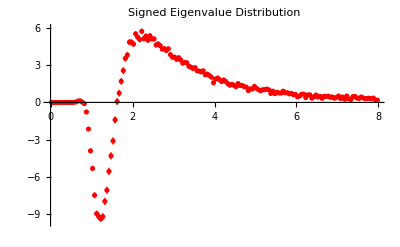

```mathematica
list=Import["/Users/oist/Documents/Projects/TensorEigenvalues & Glasses/Tensor Eigenvalues/NaokiTensorEigenvalues/signedv2L12samp10000b01.m"];
(* Analysis of data *)

wmax=8; (* The range of |v| to see *)
dw=.05; (* Bin size *)

binmax=Ceiling[wmax/dw];

(*
histo=Table[0,{binmax}];
*)
histop=Table[0,{binmax}];
histom=Table[0,{binmax}];


Do[
vert=Ceiling[list[[datnum,1]]/dw];

If[vert<=binmax,

kval=list[[datnum,2]];

Which[kval>0,histop[[vert]]+=1,True,histom[[vert]]+=1];

(*
histo[[vert]]+=kval;
*)

];

,{datnum,1,Length[list]}];

histo=Table[Around[histop[[i]]-histom[[i]],Sqrt[histop[[i]]+histom[[i]]]],{i,1,Length[histop]}];

histo/=sampnum;

newhisto=Table[{dw(i-1/2),histo[[i]]/dw},{i,1,Length[histo]}];

histoPlot=ListPlot[Map[{1,1}*# &,newhisto],PlotRange->All,PlotStyle->Red,PlotLabel->"Signed Eigenvalue Distribution"]
```

## 3. Plots: Analytics vs numerics

General::munfl: Exp[-2.80805×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

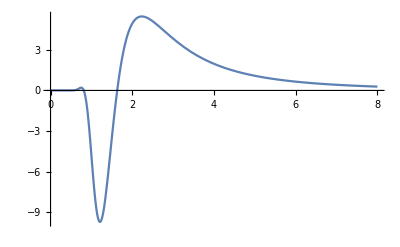

```mathematica
analPlot=Plot[rhoRadial[v,0.1,L,1/2],{v,0,8},PlotRange->All]
```

```mathematica
,AxesLabel->{Style["v",16],Style["ρ_s^size(v)",16]}
```

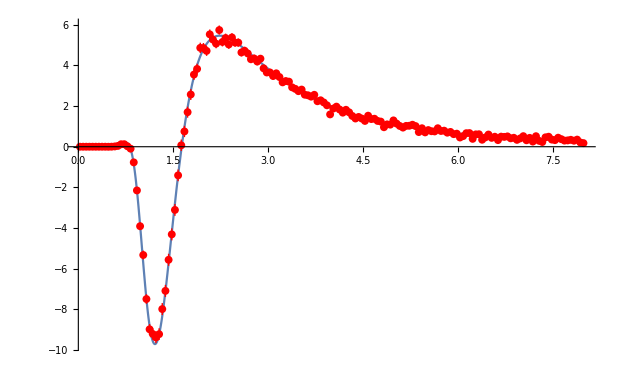

```mathematica
Show[analPlot,histoPlot]
```

## 4. Lefschetz thimbles (optional)

How did the contour for x=2 was obtained?

## 5. Appendix B